## Can We Survive By Flying Down The Building With A Bed Sheet?

Here is the thing, I don’t know exactly how to calculate the resistance of a bed sheet. So EVERYTHING I do here is just approximation.

一个物体降落的时候受到的空气阻力（在速度比较快的时候）可以用 1/2 ρ_air C_d A v^2来估算。其中 ρ_air是空气密度，大约为 1.22 kg/m^3， C_d是用来表征物体形状的一个系数，降落伞的话是大致取 0.75，因为降落伞实际上有效的投影面积乘上降落伞形状带来的因素差不多是这个值，但是我们的床单可能是需要取在 0.6~0.8之间，具体情况需要一些更详细的推导。A是床单的面积，展开面积。

但是速度比较小的时候，物体下落的时候空气阻力可以用  b A v 来计算，并且我们有：
机翼那种形状的 0.2，球形的 0.5，平板是1.28

只是抛砖引玉，我给一个大致的下落速度范围吧。假定体重是 50kg。

#### 使用速度平方的形式（对于高速情况更准确些）

如果下落的距离很远，下落终将达到稳定速度。我们先来看看这个最终的稳定速度会是多少。

如果取 Cd=0.5

```mathematica
shapeFact2[a_]=√(2*50*9.8/(1.22*0.6 a));
```

如果取 Cd=1

```mathematica
shapeFact1[a_]=√(2*50*9.8/(1.22* 0.8 a));
```

如果取 Cd=0.75

```mathematica
shapeFact[a_]=√(2*50*9.8/(1.22*0.7 a));
```

这样我们就可以计算了。

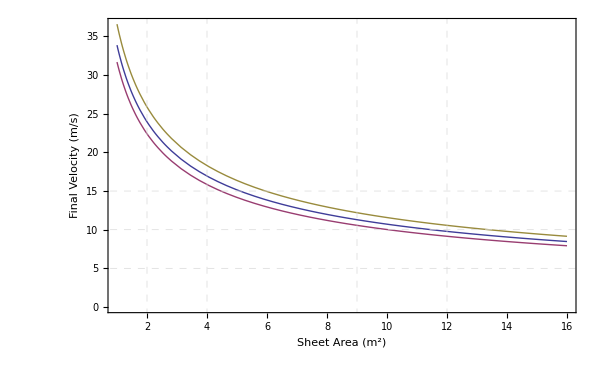

```mathematica
Plot[{shapeFact[a],shapeFact1[a],shapeFact2[a]},{a,1,16},AxesOrigin->{1,0},PlotRange->{{1,16},Automatic},Frame->True,FrameLabel->{"Sheet Area (m^2)","Final Velocity (m/s)"},GridLines->{{{2,Dashed},{4,Dashed},{9,Dashed},{12,Dashed}},{{15,Dashed},{10,Dashed},{5,Dashed}}},ImageSize->600]
```

基本上，用单人床的床单，往最好的情况想，床单没有弯曲，2*2 平方米这么大的，落地后的速度在十几米每秒这样。这比被五六十千米每小时的车撞还严重。

上面这只是给大家看看，下面我们要具体的计算一下。为什么要计算一下呢，因为实际上我们上面给出的是很久之后的速度，一般是十几，几十秒之后才能达到这样的速度。但是我们跳楼的时候，基本上在两秒内完成了……

我们可以直接把速度解出来。

```mathematica
vel[Cd_,A_,m_,t_]=v[t]/.DSolve[{v[0]==0,D[v[t],t]==g-(ρ Cd A)/(2m) (v[t])^2},v[t],t][[1]]/.{g->9.8,ρ->1.22}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(4.00819 √m Tanh[(2.44499 √A √Cd t)/(√m)])/(√A √Cd)

```mathematica
height[Cd_,A_,m_,t_]=Integrate[vel[Cd,A,m,t],t]
```

(1.63934 m Log[Cosh[(2.44499 √A √Cd t)/(√m)]])/(A Cd)

```mathematica
time[Cd_,A_,m_,building_]=t/.Solve[height[Cd,A,m,t]==building,t][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(0.408999 √m ArcCosh[1. ⅇ^((0.61 A building Cd)/m)])/(√A √Cd)

```mathematica
time[1,1,50,10]
```

1.45779

```mathematica
√(20/9.8)
```

1.42857

```mathematica
velEnd[Cd_,A_,m_,building_]=vel[Cd,A,m,time[Cd,A,m,building]]
```

(4.00819 √m Tanh[1. ArcCosh[1. ⅇ^((0.61 A building Cd)/m)]])/(√A √Cd)

```mathematica
velEnd[1,1,50,1]
```

4.40032

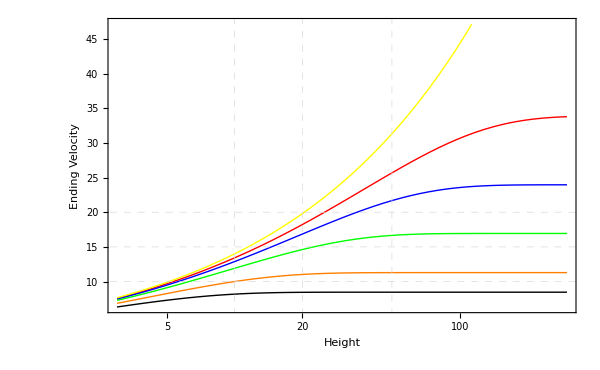

```mathematica
pltVelVSHeight=LogLinearPlot[{velEnd[0.7,1,50,h],velEnd[0.7,2,50,h],velEnd[0.7,4,50,h],velEnd[0.7,9,50,h],velEnd[0.7,16,h],√(2 9.8 h)},{h,3,300},PlotStyle->{Red,Blue,Green,Orange,Black,Yellow},Frame->True,FrameLabel->{"Height","Ending Velocity"},GridLines->{{{10,Dashed},{20,Dashed},{50,Dashed}},{{10,Dashed},{15,Dashed},{20,Dashed}}},PlotLabel->"",ImageSize->600]
```

从上到下，分别是面积为1，2，4，9，16的情况，这里近似认为使用床单是 Cd=0.7。最上面那条黄线是自由落体……

这样看来，基本上，如果床单面积达到了16平米，那就问题不大了，从哪里跳下来都还算安全。不过想想那得多大的床单……
对于9平米的床单，也还可以，看橘色的线，问题也不大，最多 10 m/s 的样子，姿势正确似乎也不会很致命，就像百米冲刺的速度撞墙，唔，好疼。

而对于我们的正常的床单， 面积最大在4平米左右，看绿色的线，在20米左右的高度的楼房上跳下来，会达到17米每秒，这样很危险了，不过总比没有床单好，因为没有床单会达到 20 m/s。

如果床单的面积在 2 平米左右（1*2，单人床的各位），这时再跳就危险了，如果房子足够高，例如达到了50米的高度，最后速度可以达到25米每秒，比被90多千米每小时的车撞还厉害。当然我们的房子大多每那么高，例如在20米高的地方跳下来，那速度也会有18米每秒。危险。

还可以注意到，对于那些那些1或2平米的床单，在10m之内跳楼都基本不起作用，跟直接跳下来也差不了多少。

而且这些是最理想的情况，具体最大效果需要把床单最大程度的展开。这上面估算的情况是让床单像降落伞一样弯曲的时候，如果能够让床单整个平整的展开，拖拽效果更好些，不过这时候需要注意稳定性。
以上换成窗帘同样成立，窗帘更大些。

#### 其它体重

我们来看看看体重的影响。为了简便起见，我们使用 Cd=0.7，A=4或9（窗帘的面积吧）。

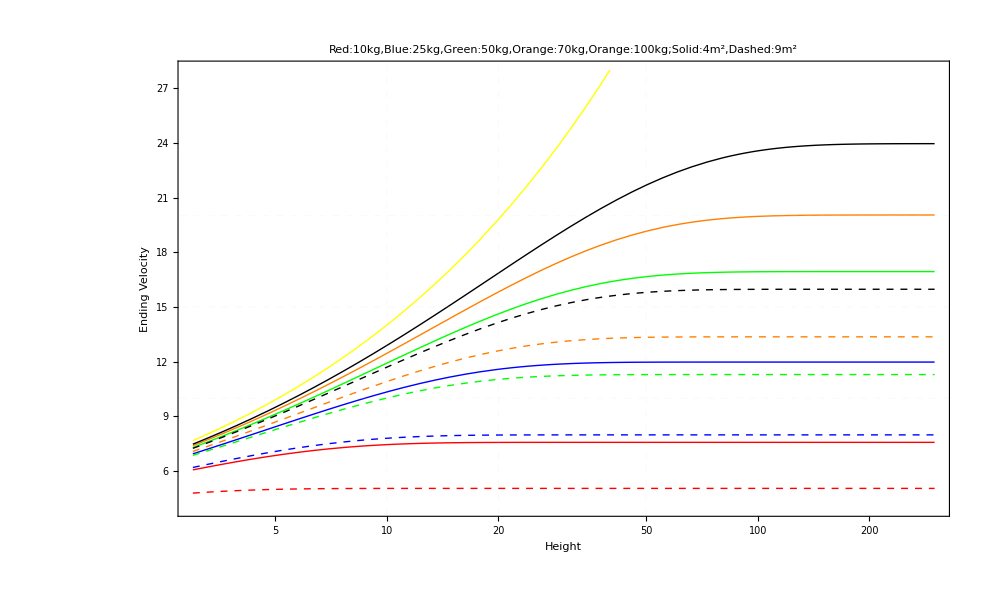

```mathematica
pltVelVSHeightM=LogLinearPlot[{velEnd[0.7,4,10,h],velEnd[0.7,4,25,h],velEnd[0.7,4,50,h],velEnd[0.7,4,70,h],velEnd[0.7,4,100,h],velEnd[0.7,9,10,h],velEnd[0.7,9,25,h],velEnd[0.7,9,50,h],velEnd[0.7,9,70,h],velEnd[0.7,9,100,h],√(2 9.8 h)},{h,3,300},PlotStyle->{Red,Blue,Green,Orange,Black,Directive[Red,Dashed],Directive[Blue,Dashed],Directive[Green,Dashed],Directive[Orange,Dashed],Directive[Black,Dashed],Yellow},Frame->True,FrameLabel->{"Height","Ending Velocity"},GridLines->{{{10,Directive[Opacity[0.2],Dashed]},{20,Directive[Opacity[0.2],Dashed]},{50,Directive[Opacity[0.2],Dashed]}},{{10,Directive[Opacity[0.2],Dashed]},{15,Directive[Opacity[0.2],Dashed]},{20,Directive[Opacity[0.2],Dashed]}}},PlotLabel->"Red:10kg,Blue:25kg,Green:50kg,Orange:70kg,Orange:100kg;Solid:4m^2,Dashed:9m^2",PlotRange->{Automatic,{4,28}},ImageSize->700]
```

红蓝绿橙黑分别是体重为 10kg,25kg,50kg,70kg,100kg 的情况。实线是窗帘面积为4平米，虚线是窗帘面积为9平米。黄线还是自由落体。

体重在这里扮演了很重要的角色。如果是一个小孩子，体重 10kg，那么 9平米的窗帘甚至可以让小孩子以 5m/s 以下的速度落地。但是如果体重达到了 100kg，那么即便是 9 平米的窗帘也不安全，因为速度达到了 15m/s 的。
其它想要知道的可以从图中读出来。但总体而言，这个问题里面体重很重要，越是轻的人，落地速度越小，尤其是从比较高的地方跳下来的时候。

### 阻力正比于速度

一般大家都是按照上面的方法来算的。我无法从最基本开始推导出上面的阻力公式，所以我一直认为这都是经验公式。至于速度是多少的时候是怎么表达，我不清楚，需要一些实验。不过可以知道的是，虽然在速度小的时候认为阻力正比于速度更合理些，但是差别不会太大。这里只是为了全面，顺手算一下。

## Draft

### 对于平方正比情况的估算方法

既然是估算，对于我们跳楼这种在两秒内完成的事情，可以用这个解的三阶近似。

```mathematica
Series[vel[Cd,A],{t,0,4}]
```

9.8 t-0.390563 (A Cd) t^3+O[t]^5

```mathematica
velApp[Cd_,A_,t_]=9.8 t-0.39056266666666667 (A Cd) t^3
```

9.8 t-0.390563 A Cd t^3

画图来验证一下这个估算到底在什么情况下合适。

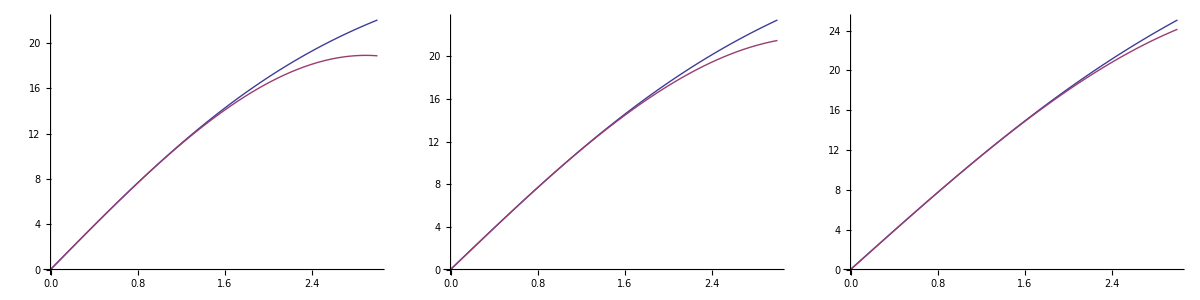

```mathematica
Grid[{{Plot[{vel[1,1,t],velApp[1,1,t]},{t,0,3}],Plot[{vel[0.75,1,t],velApp[0.75,1,t]},{t,0,3}],Plot[{vel[0.5,1,t],velApp[0.5,1,t]},{t,0,3}]}}]
```

这样看来，在两秒内这个近似很好，三秒内还凑合。那么两秒我们落了多高呢？

```mathematica
heightApp[Cd_,A_,t_]=Integrate[velApp[Cd,A,t],t]
```

4.9 t^2-0.0976407 A Cd t^4

```mathematica
heightApp[1,1,2]
heightApp[0.75,1,2]
heightApp[0.5,1,2]
```

18.0377

18.4283

18.8189

也就是落了18米了。

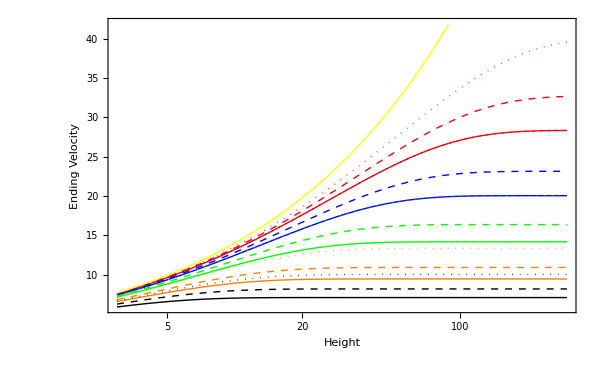

```mathematica
pltVelVSHeightTEST=LogLinearPlot[{velEnd[1,1,h],velEnd[1,2,h],velEnd[1,4,h],velEnd[1,9,h],velEnd[1,16,h],velEnd[0.75,1,h],velEnd[0.75,2,h],velEnd[0.75,4,h],velEnd[0.75,9,h],velEnd[0.75,16,h],velEnd[0.5,1,h],velEnd[0.5,2,h],velEnd[0.5,4,h],velEnd[0.5,9,h],velEnd[0.5,16,h],√(2 9.8 h)},{h,3,300},PlotStyle->{Red,Blue,Green,Orange,Black,Directive[Red,Dashed],Directive[Blue,Dashed],Directive[Green,Dashed],Directive[Orange,Dashed],Directive[Black,Dashed],Directive[Red,Dotted],Directive[Blue,Dotted],Directive[Green,Dotted],Directive[Orange,Dotted],Directive[Black,Dotted],Yellow},Frame->True,FrameLabel->{"Height","Ending Velocity"},ImageSize->600]
```

从上到下，分别是面积为1，2，4，9，16的情况。实线是 Cd=1，Dashed 是 Cd=0.75，Dotted点线是 Cd=0.5。最上面那条黄线是自由落体……

这样看来，基本上，如果床单在空中展开的面积达到了16平米，那就问题不大了，从哪里跳下来都还算安全。不过想想那得多大的床单……
对于9平米的床单，也还可以，因为实际上如果降落伞的 Cd =0.75 的话，那床单也差不多这个值。这样的话，如果展开的面积达到 9 平米，那跳下来看橘色的 Dashed 线，问题也不大，最多 10 m/s 的样子，姿势正确似乎也不会很致命，就像百米冲刺的速度撞墙，唔，好疼。

而对于我们的正常的床单， 面积最大在4平米左右，看绿色的线 Dashed，在20米左右的高度的楼房上跳下来，会达到15米每秒之下，这样很危险了，不过总比没有床单好。

如果考虑弯曲，那床单的有效面积小多了，甚至可能在 2 平米左右，这时，机器危险了，如果房子足够高，例如达到了50米的高度，最后速度可以达到20米每秒，比被70多千米每小时的车撞还厉害。当然我们的房子大多每那么高，例如在20米高的地方跳下来，那速度也会有15米每秒以上。

```mathematica
Plot[{func[a],func1[a],func2[a]},{a,1,16},AxesOrigin->{1,0},PlotRange->{{1,16},Automatic},GridLines->{{},{{10,Dashed},{5,Dashed}}}]
```